```mathematica
h[x_]:=Piecewise[{{1+Subscript[c, 0,1] x+Subscript[c, 0,2] x^2+Subscript[c, 0,3] x^3, 0≤x≤1/2}, {Subscript[c, 1,1](x-1)+Subscript[c, 1,2](x-1)^2+Subscript[c, 1,3](x-1)^3, 1/2<x≤3/2}, {Subscript[c, 2,1](x-2)+Subscript[c, 2,2](x-2)^2+Subscript[c, 2,3](x-2)^3, 3/2<x≤5/2}, {0, True}}];
f[x_]:=h[Abs[x]];
AllVars={Subscript[c, 0,1],Subscript[c, 0,2],Subscript[c, 0,3],Subscript[c, 1,1],Subscript[c, 1,2],Subscript[c, 1,3],Subscript[c, 2,1],Subscript[c, 2,2],Subscript[c, 2,3]};
```

```mathematica
(*Continuity*)
C1=Limit[h[x],x->1/2,Direction->1]==Limit[h[x],x->1/2,Direction->-1]
C2=Limit[h[x],x->3/2,Direction->1]==Limit[h[x],x->3/2,Direction->-1]
C3=Limit[h[x],x->5/2,Direction->1]==Limit[h[x],x->5/2,Direction->-1]
```

1/8 (8+4 c_(0,1)+2 c_(0,2)+c_(0,3))==1/8 (-4 c_(1,1)+2 c_(1,2)-c_(1,3))

1/8 (4 c_(1,1)+2 c_(1,2)+c_(1,3))==1/8 (-4 c_(2,1)+2 c_(2,2)-c_(2,3))

1/8 (4 c_(2,1)+2 c_(2,2)+c_(2,3))==0

```mathematica
(*Partition of unity and linear term*)
T0=CoefficientList[FullSimplify[∑_(i=-6)^6 f[x-i],x>0&&x<1/2],x]
T1=CoefficientList[FullSimplify[∑_(i=-6)^6 i f[x-i],x>0&&x<1/2],x]
```

{1,c_(0,1),c_(0,2)+2 (c_(1,2)+c_(2,2)),c_(0,3)}

{0,-2 c_(1,1)-4 c_(2,1),0,-2 (c_(1,3)+2 c_(2,3))}

```mathematica
GenSols=Solve[{
	C1,C2,C3,
	T0[[2]]==0,
	T0[[3]]==0,
	T0[[4]]==0,
	T1[[2]]==1,
	T1[[4]]==0
	},
	AllVars
]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{c_(0,1)→0,c_(0,3)→0,c_(1,2)→1,c_(1,3)→-6-2 c_(0,2)-4 c_(1,1),c_(2,1)→-1/4-(c_(1,1))/2,c_(2,2)→-1-(c_(0,2))/2,c_(2,3)→3+c_(0,2)+2 c_(1,1)}}

```mathematica
RegionXY[k_]:={Quotient[k,2],1+Quotient[-k,2]};
Regions=Table[RegionXY[k],{k,-4,7}]-1/2
```

{{-5/2,5/2},{-5/2,3/2},{-3/2,3/2},{-3/2,1/2},{-1/2,1/2},{-1/2,-1/2},{1/2,-1/2},{1/2,-3/2},{3/2,-3/2},{3/2,-5/2},{5/2,-5/2},{5/2,-7/2}}

```mathematica
GenSol=GenSols[[1]];
f[x_,y_]:=f[x]f[y];
φ=1/2;
W[k_]:=Piecewise[{{0, k<0}, {φ^2/2, k==0}, {1-(1-φ)^2/2, k==1}, {1, True}}];
SumF=∑_(i=-5)^6 ∑_(j=-5)^6 W[i-j]f[x-i,y-j]/.GenSol;
SimplifySquare[f_,x0_,y0_]:=Simplify[f,x>x0&&x<x0+1&&y>y0&&y<y0+1];
DSimplifySquare[f_,{x0_,y0_}]:=Simplify[D[SimplifySquare[f,x0,y0],{{x,y}}]];
DSumF=ParallelMap[DSimplifySquare[SumF,#]&,Regions];
```

```mathematica
AnisoInt[df_,{x0_,y0_}]:=Simplify[Integrate[Expand[(df.{1,1})^2],{x,x0,x0+1},{y,y0,y0+1}]];
AnisoInts=Parallelize[MapThread[AnisoInt,{DSumF,Regions}]];
Err=Simplify[Total[AnisoInts]]
```

1/12902400(638955 c_(0,2)^4+c_(0,2)^3 (7449812-12024 c_(1,1))+12 c_(0,2)^2 (3036379+10590 c_(1,1)+14088 c_(1,1)^2)+96 c_(0,2) (786959+109083 c_(1,1)+40016 c_(1,1)^2+2012 c_(1,1)^3)+96 (633789+311236 c_(1,1)+140734 c_(1,1)^2+8388 c_(1,1)^3+8048 c_(1,1)^4))

```mathematica
FreeVars=Variables[Err];
DErr=Simplify[D[Err,{FreeVars}]];
H=D[DErr,{FreeVars}];
Sols=Solve[DErr==0,FreeVars,Reals];
TableForm[{Range[Length[Sols]],Err/.N[Sols],PositiveDefiniteMatrixQ[H/.N[#]]&/@Sols}ᵀ]
```

1 | 0.0902019 | True

```mathematica
RootReduce[Sols[[1]]]
```

{c_(0,2)→Root[95847501175547613564801600+290787026673489172616069184 #1+427693530277085972126756216 #1^2+374454369419578668527648440 #1^3+206526493409660806096287626 #1^4+73985811686932641040952616 #1^5+17333088289108701496879625 #1^6+2585430622222421745766995 #1^7+224999970811293497663025 #1^8+8794043350198430409225 #1^9&,1],c_(1,1)→Root[186034729797937411538022907705+266195094834401033071061383245 #1+23814746789073430925129080750 #1^2-74579241765856896300539908358 #1^3-31992383923550463074170477624 #1^4+27118665196708626294219280904 #1^5+12658942797006126318184281760 #1^6+12703022498519592874591024320 #1^7+1336110826973695570314316800 #1^8+1509855165491135315913446400 #1^9&,1]}

{c_(0,1)→0,c_(0,3)→0,c_(1,2)→1,c_(1,3)→0.463315,c_(2,1)→0.162576,c_(2,2)→-0.209324,c_(2,3)→-0.231657,c_(0,2)→-1.58135,c_(1,1)→-0.825153}

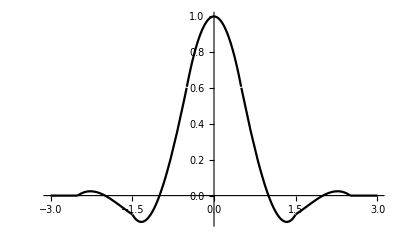

```mathematica
NSol=N[Sols[[1]]];
FullSol=Join[GenSol/.NSol,NSol]
fo[x_]:=f[x]/.FullSol;
Plot[fo[x],{x,-3,3},PlotStyle->Black,Background->White]
```